Did the first part of this in class on a whiteboard, then again with John on a whiteboard, then a third time with Brian on a whiteboard. Not worth writing out a fourth time, but here’s some analysis. Curve fits real nice and gives reasonable results for lumped constants, corroborating this model for the system.

```mathematica
data=Import["C:\\Users\\jbriskman\\Documents\\2017 Fall\\QEA\\hothothot.csv","Data"];
```

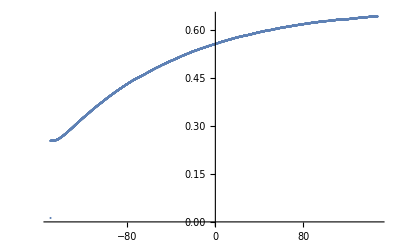

```mathematica
ListPlot[data]
```

```mathematica
diffeq=Q*T'[t] == V^2/R-Subscript[C, p] T[t]
```

Q T'[t]==V^2/R-C_p T[t]

```mathematica
data$clean=Cases[data,{t_/;t>-147,T_}:>{t+147,(T-.254)*100}]
```

{{0.0375,0.0704486},{0.075,0.0704486},{0.1125,0.0704486},{0.15,0.0704486},{0.1875,0.0704486},{0.225,0.0704486},7843,{294.375,38.9882},{294.413,38.9882},{294.45,38.9882},{294.488,38.9882},{294.525,38.9882}}
 |  |  |  |

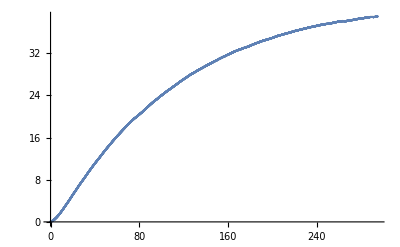

```mathematica
ListPlot[data$clean]
```

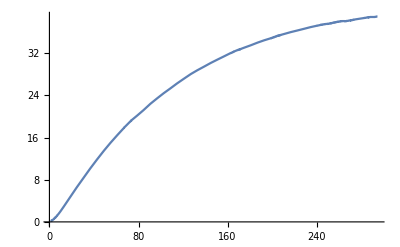

```mathematica
f=Interpolation[data$clean];
Plot[f[t],{t,1,data$clean[[-1,1]]}]
```

```mathematica
sol=DSolveValue[diffeq,T[t],t]
```

ⅇ^(-(t C_p)/Q) C[1]+V^2/(R C_p)

```mathematica
eq=sol/.{C[1]->c1,Subscript[C, p]->cp,V->9,R->50}
params=FindFit[data$clean,eq,{{c1},{cp,10},{Q,10}},t]
```

81/(50 cp)+c1 ⅇ^(-(cp t)/Q)

{c1→-44.4132,cp→0.0378922,Q→4.3845}

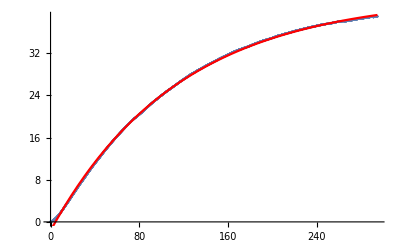

```mathematica
Show[ListPlot[data$clean],Plot[eq/.params,{t,1,data$clean⟦-1,1⟧},PlotStyle->Red]]
```

```mathematica
data$clean[[-1]]
```

{294.525,38.9882}